# Deterministic population size dynamics

## Single population constant size

```mathematica
Clear["Global`*"]
```

## Population size over time

```mathematica
Pars={R->0.2,κ->1000,tmax->500, μ->10^-6,nSites->200};
```

```mathematica
Clear[n];
n[t_]:=κ;
```

Plotting population size over time:

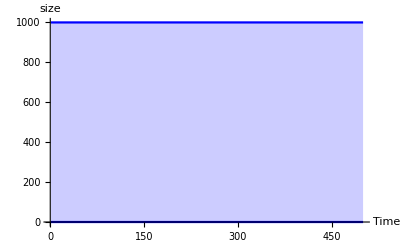

```mathematica
PopSize=ListLinePlot[{Table[{t,κ/2+n[t]/2/.Pars},{t,1,tmax/.Pars}],Table[{t,κ/2-n[t]/2/.Pars},{t,1,tmax/.Pars}]},Filling->{1->{{2},Directive[Blue,Opacity[0.2]]}},PlotStyle->{Blue,Blue},AxesLabel->{"Time","size"}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/popSize_S0.pdf",PopSize]
```

/Users/ailenemacpherson/Documents/OutPut/popSize_S0.pdf

## Predicted Coalescent Times

### Base probability distribution

The coalescent times follow the standard coalescent, so given that m lineages are sampled at time zero the joint probability that the coalescent times to the common ancestors is a vector τ={0,τ2,τ3,...τm} is given by:

```mathematica
G[τ_,m_]:=Product[Binomial[j,2]Exp[-Binomial[j,2]τ[[j]]],{j,2,m}]
```

Plotting this distribution for m=3 gives:

```mathematica
GDist[3]:=Block[{κκ,pts,dist,i,j},κκ=κ/.Pars;dist={};
pts=N[Flatten[Table[{0,i/κκ,j/κκ},{i,0,2κκ,5},{j,0,2κκ,5}],1]];
For[j=1,j≤Length[pts],j++,
AppendTo[dist,Join[pts[[j,2;;3]],{G[pts[[j]],3]}]];
];
dist
]
```

```mathematica
GPlot=ListPlot3D[GDist[3],PlotRange->All,AxesLabel->{"τ2","τ3","Prob"}]
```

-Graphics3D-

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/GPlot_S0.pdf",GPlot]
```

/Users/ailenemacpherson/Documents/OutPut/GPlot_S0.pdf

### Conditional Probability distribution

I know want to find the conditional probability that the most recent common ancestor is reached before time (in coalescent units) T.  This is not as straightforward as obtaining some conditional probability distributions because the coalescent events must occur in sequence.  To calculate this joint conditional probability distribution I begin by calculating the probability that j lineages coalesce to j-1 lineages at time τ given that they coalesce before time Tm. This is simply the truncated exponential distribution.

```mathematica
gc[j_,τ_,Tm_]:=(Binomial[j,2]Exp[-Binomial[j,2]τ])/(1-Exp[-Binomial[j,2]Tm])
```

Hence the complete conditional probability that you observe coalescent times τ={0,τ2, τ3,...τm}.

```mathematica
Gc[τ_,m_,Tm_]:=If[Total[τ]>Tm,0,Product[gc[j,τ[[j]],Tm-Sum[τ[[k]],{k,j+1,m}]],{j,2,m}]]
```

Plotting the resulting conditional probability distribution

```mathematica
GDistc[3,Tm_]:=Block[{κκ,pts,dist,i,j},κκ=κ/.Pars;dist={};
pts=N[Flatten[Table[{0,i/κκ,j/κκ},{i,1,2κκ,5},{j,1,2κκ,5}],1]];
For[j=1,j≤Length[pts],j++,
AppendTo[dist,Join[pts[[j,2;;3]],{Gc[pts[[j]],3,Tm]}]];
];
dist
]
```

```mathematica
GconPlot=ListPlot3D[GDistc[3,2],PlotRange->All,AxesLabel->{"τ2","τ3","Prob"}]
```

-Graphics3D-

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/GconPlot_S0.pdf",GconPlot]
```

/Users/ailenemacpherson/Documents/OutPut/GconPlot_S0.pdf

## Simulated Coalescent Times

### Plotting Single coalescent sample:

Plotting the coalescent tree

```mathematica
rep=1;
cdata=Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/case00/coal0_",ToString[rep],".csv"]][[;;,1;;-2]];
nLinF=cdata[[-1,-1]];
tTotal=Length[cdata];
```

```mathematica
CoalPlot[mF_]:=Block[{sample,csample,ndist},
sample=RandomChoice[Range[0,nLinF],mF]+1;
csample=cdata[[;;,sample]];
ndist=Table[CountDistinct[csample[[k]]],{k,1,tTotal}];
Print[Table[{l,Count[ndist,l]},{l,1,mF}]];
Show[Table[ListLinePlot[Transpose[{Range[tTotal],Transpose[csample][[j]]}]],{j,1,mF}],ListPlot[Table[{Sum[Count[ndist,k],{k,1,l-1}],0},{l,1,mF}],PlotStyle->Red]]
]
```

{{1,64},{2,108},{3,30}}

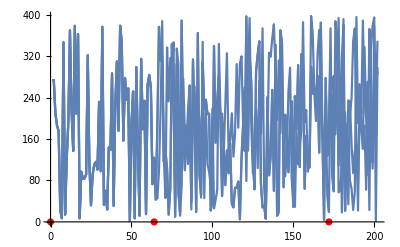

```mathematica
test=CoalPlot[3]
```

### Distribution of coalescent times

```mathematica
nRep=5000;
nLinF=2n[(tmax/.Pars)+2]/.Pars;
tTotal=(tmax/.Pars)+2;
```

```mathematica
CoalTimes[mF_,m0_]:=Block[{cdata,sample,csample,ndist,ctimes},ctimes={};
For[r=1,r≤nRep,r++,
cdata=Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/Case00/coal0_",ToString[r],".csv"]][[;;,1;;-2]];
sample=RandomChoice[Range[1,nLinF],mF];
csample=cdata[[;;,sample]];
ndist=Table[CountDistinct[csample[[k]]],{k,1,tTotal}];
AppendTo[ctimes,Table[Count[ndist,l],{l,m0+1,mF}]];
];
ctimes=Select[ctimes,Total[#]<tTotal&]
(*N[ctimes/(κ/.Pars)]*)
]
```

```mathematica
test=CoalTimes[3,1];
```

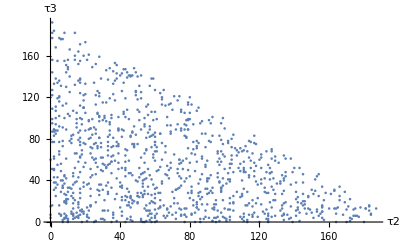

```mathematica
ListPlot[test,AxesLabel->{"τ2","τ3"}]
```

```mathematica
Histogram3D[test]
```

-Graphics3D-

## Predicted pairwise differences

I am going to calculate the expected number of pairwise differences under the infinite sites model.  This model is not strictly true in our simulaitons but will be approximately so as long as the per base pair mutation rate is low enough. The expected number of pairwise differences (in a infinite sites model) depends on the time over which two lineages can diverge.  Given that the lineages are constrained to being identical at the beginning of the simulation the maximum divergence time is 2(Tmax).  However if lineages coalesce before the beginning of the simulation the divergence time will be less.  If I define an accurate approximation to the infinite sites model to be the probability that a mutation occurs at the same site over 2Tmax units of time to be pmax then the necessary maximum per base pair mutation rate is: This is wrong see summary

```mathematica
μmax[pmax_]:=pmax/(2(tmax/.Pars))
```

```mathematica
μmax[0.01]//ScientificForm
```

1.×10^-5

Given that the mutation rate is less than or equal to this than we can calculate the expected number of pairwise differences as follows.  1) Calculate the divergence time between two lineages and 2) calculate the expected number of difference given divergence time.

The time separating 2 lineages:  As mentioned above lineages either never coalesce or the coalesce at time t<Tmax

```mathematica
Tdiverg=2(tmax/κ Exp[-tmax/κ]+Sum[l/κ (1/κ Exp[-l/κ]),{l,1,tmax}])/.Pars//N
```

0.787242

The expected number of mutations that arise per coalescent generation is, θ (note this is 1/2 the classical use of theta) is:

```mathematica
θ=nSites μ κ/.Pars//N
```

0.2

Hence the expected number of pairwise differences is:

```mathematica
Tdiverg θ
```

0.157448

## Single population logistic growth:

```mathematica
Clear["Global`*"]
```

## Population size over time

```mathematica
Pars={R->0.2,κ->200,tmax->200};
```

```mathematica
Clear[n];
n[0.0]=n[0]=(*κ/.Pars*)Floor[(κ/50/.Pars)];
n[t_]:=If[t<0,κ/.Pars,
n[t]=Round[(n[t-1]+n[t-1] R(1-n[t-1]/κ))/.Pars]]
```

Plotting population size over time:

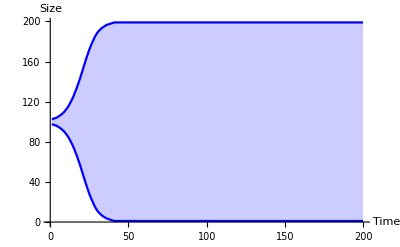

```mathematica
PopSize=ListLinePlot[{Table[{t,κ/2+n[t]/2/.Pars},{t,1,tmax/.Pars}],Table[{t,κ/2-n[t]/2/.Pars},{t,1,tmax/.Pars}]},Filling->{1->{{2},Directive[Blue,Opacity[0.2]]}},PlotStyle->{Blue,Blue},AxesLabel->{"Time","Size"}]
```

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/popSize_S1.pdf",PopSize]
```

/Users/ailenemacpherson/Documents/OutPut/popSize_S1.pdf

## Predicted Coalescent Times (Griffiths and Tavare)

The joint probability distribution of coalescent times is given by G[τ] where τ is a vector of coalescent times τ={τ2,τ3,...τm} where m is the number of sampled lineages.

### Base distribution of coalescent times

Let

The distribution of coalescent times from m lineages to a common ancestor is given by:

```mathematica
G[τ_,m_]:=Block[{ttmax,κκ}, ttmax=tmax/.Pars;κκ=κ/.Pars;N[Product[Binomial[j,2](κκ/n[ttmax-Sum[κκ τ[[k]],{k,j,m}]])Exp[-Binomial[j,2](Sum[1/n[ttmax-l],{l,Sum[κκ τ[[k]],{k,j+1,m}],Sum[κκ τ[[k]],{k,j,m}]}])],{j,2,m}]]
]
```

Plotting the resulting distribution of coalescent times where m=3

```mathematica
GDist[3]:=Block[{pts,sampSize,dist,j},dist={};
N[pts=Flatten[Table[{0,t2/(κ/.Pars),t3/(κ/.Pars)},{t2,1,(tmax/.Pars),2},{t3,1,(tmax/.Pars)-t2,2}],1]];
For[j=1,j≤Length[pts],j++,
AppendTo[dist,Join[pts[[j,2;;3]],{G[pts[[j]],3]}]]
];
N[dist]
]
```

```mathematica
temp=GDist[3];
```

```mathematica
GPlot=ListPlot3D[temp,PlotRange->All,AxesLabel->{"τ2","τ3","Prob"}]
```

-Graphics3D-

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/GPlot_S1.pdf",GPlot]
```

/Users/ailenemacpherson/Documents/OutPut/GPlot_S1.pdf

### Conditional probability distribution

I now want to calculate the conditional probability of observing coalescent times in the vector τ.  To do this we begin by calculating the probability of a coalescent event between j lineages before time T (measured in coalescent time) before the present.

```mathematica
pdfj[τ_,j_]:=Block[{ttmax,κκ,m,prob}, ttmax=tmax/.Pars;κκ=κ/.Pars;m=Length[τ];
If[Total[τ[[j;;m]]]>ttmax/κκ,prob=0;,
prob=Binomial[j,2](κκ/n[ttmax-Sum[κκ τ[[k]],{k,j,m}]])Exp[-Binomial[j,2](Sum[1/n[ttmax-l],{l,Sum[κκ τ[[k]],{k,j+1,m}],Sum[κκ τ[[k]],{k,j,m}]}])];
];
N[prob]
]
```

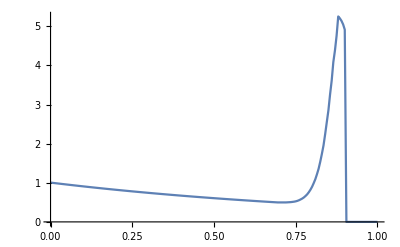

```mathematica
ListLinePlot[Table[{N[t],pdfj[{0,t,0.1},2]},{t,0,tmax/κ/.Pars,1/κ/.Pars}],PlotRange->All]
```

The cumulative probability distribution of j lineages coalessing before time T is the following.  Note that this distribution depends on the vector of coalescent times as coalescent times are are no longer independent.

```mathematica
cdfj[τ_,j_,T_]:=Block[{ttmax,κκ,m,prob,k,τp}, ttmax=tmax/.Pars;κκ=κ/.Pars;
prob=0;
For[k=1,k≤κκ T,k++,
τp=N[ReplacePart[τ,j-> k/κκ]];
prob+=1/κκ pdfj[τp,j];
];
N[prob]
]
```

```mathematica
pdfj[{0,0.92,0.1},2]
```

0.

```mathematica
cdfj[{0,0,0.1},2,1/κ/.Pars]
```

0.00499975

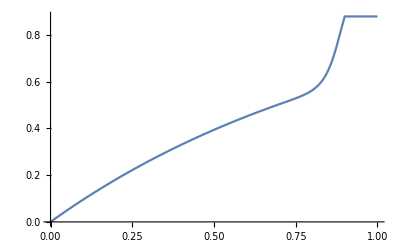

```mathematica
ListLinePlot[Table[{t,cdfj[{0,0,0.1},2,t]},{t,0,1,1/(κ/.Pars)}],PlotRange->All]
```

```mathematica
gc[T_,τ_,j_]:=Block[{ttmax,κκ,m,prob}, ttmax=tmax/.Pars;κκ=κ/.Pars;m=Length[τ];
If[Total[τ[[j;;m]]]>T,prob=0,prob=pdfj[τ,j]/cdfj[τ,j,T-Total[τ[[j+1;;m]]]]];
prob
]
```

```mathematica
gc[tmax/κ/.Pars,{0,0.2,0.2},2]
```

0.948233

The related joint conditional probability distribution of observing coalescent times τ={τ_m,τ_(m-1),...,τ_2} is given by:

```mathematica
Gc[T_,τ_,m_]:=Block[{gout},If[Total[τ]>T,gout=0,gout=Product[gc[T,τ,j],{j,2,m}]]]
```

```mathematica
τTest={0,0.7,0.2};
```

```mathematica
Gc[1,τTest,3]
```

1.92339

Plotting resulting conditional probability distribution for m=3

```mathematica
GcDist[3]:=Block[{pts,sampSize,dist,j,κκ,ttmax},dist={};κκ=κ/.Pars;ttmax=tmax/.Pars;
pts=N[Flatten[Table[{0,t2/κκ,t3/κκ},{t2,1,1 κκ,5},{t3,1,1 κκ,5}],1]];
For[j=1,j≤Length[pts],j++,
AppendTo[dist,Join[pts[[j,2;;3]],{Gc[ttmax/κκ,pts[[j]],3]}]]
];
dist
]
```

```mathematica
temp=GcDist[3];
```

```mathematica
GconPlot=ListPlot3D[temp,PlotRange->All,AxesLabel->{"τ2","τ3"}]
```

-Graphics3D-

```mathematica
Export["/Users/ailenemacpherson/Documents/OutPut/GconPlot_S1.pdf",GconPlot]
```

/Users/ailenemacpherson/Documents/OutPut/GconPlot_S1.pdf

```mathematica
Gc[tmax/κ/.Pars,{0,0.99,0},3]
```

16.0485

```mathematica
Gc[tmax/κ/.Pars,{0,0,0.99},3]
```

28.7366

## Simulated Coalescent Times

### Plotting Single coalescent sample:

Plotting the coalescent tree

```mathematica
rep=1;
cdata=Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/case0/coal0_",ToString[rep],".csv"]][[;;,1;;-2]];
nLinF=cdata[[-1,-1]];
tTotal=Length[cdata];
```

```mathematica
CoalPlot[mF_]:=Block[{sample,csample,ndist},
sample=RandomChoice[Range[0,nLinF],mF]+1;
csample=cdata[[;;,sample]];
ndist=Table[CountDistinct[csample[[k]]],{k,1,tTotal}];
Print[Table[{l,Count[ndist,l]},{l,1,mF}]];
Show[Table[ListLinePlot[Transpose[{Range[tTotal],Transpose[csample][[j]]}]],{j,1,mF}],ListPlot[Table[{Sum[Count[ndist,k],{k,1,l-1}],0},{l,1,mF}],PlotStyle->Red]]
]
```

{{1,13},{2,16},{3,173}}

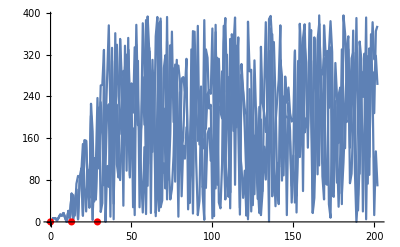

```mathematica
test=CoalPlot[3]
```

### Distribution of coalescent times

```mathematica
nRep=2000;
nLinF=2n[(tmax/.Pars)+2];
tTotal=(tmax/.Pars)+2;
```

```mathematica
CoalTimes[mF_,m0_]:=Block[{cdata,sample,csample,ndist,ctimes},ctimes={};
For[r=1,r≤nRep,r++,
cdata=Import[StringJoin["/Users/ailenemacpherson/Documents/workspace/AlleleSurfing3_13/Case0/coal0_",ToString[r],".csv"]][[;;,1;;-2]];
sample=RandomChoice[Range[1,nLinF],mF];
csample=cdata[[;;,sample]];
ndist=Table[CountDistinct[csample[[k]]],{k,1,tTotal}];
AppendTo[ctimes,Table[Count[ndist,l],{l,m0+1,mF}]];
];
ctimes=Select[ctimes,Total[#]<tTotal&]
(*N[ctimes/(κ/.Pars)]*)
]
```

```mathematica
test=CoalTimes[3,1];
```

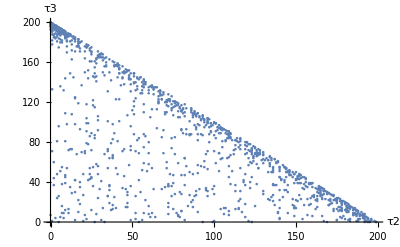

```mathematica
ListPlot[test,AxesLabel->{"τ2","τ3"}]
```

```mathematica
Histogram3D[test]
```

-Graphics3D-

## Predicted pairwise differences

The instantaneous probability that two lineages sampled at (real) time t coalesce τ coalescent units before the present is:

```mathematica
g2[τ_,t_]:=Block[{k}, k=κ/.Pars;k/n[t-k τ] Exp[-Sum[1/n[t-x k],{x,0,Floor[τ k]}]]]//N
```

The cumulative probability that 2 lineages sampled at time t coalesce on less than Tmax generations is:

```mathematica
cdf2[Tmax_,t_]:=Block[{k},k=κ/.Pars;Sum[1/k g2[x/k,t],{x,0,Tmax}]]
```

The resulting conditional probability that 2 lineages sampled at time t coalesce exactly τ coalesce units before given that they coalesce before the beginning of the simulation  is

```mathematica
f2[τ_,t_]:=g2[τ,t]/cdf2[t,t]
```

```mathematica
f2[1.0,200]
```

15.682

The expected divergence time (measured in real time units) then between two lineages sampled at time t is:

```mathematica
Tdiv[t_]:=Block[{k},k=κ/.Pars;2((1-cdf2[t,t])t+Sum[1/k f2[x/k,t]x,{x,0,t}])]
```

```mathematica
Tdiv[100]
```

105.528

The expected number of pairwise differences between two lineages sampled at time t is therefore μ Tdiv[t]. Here μ is the genome mutation rate. Note that once again there is an upper limit to μ for which it should approximate a infinite sites model.

```mathematica
S[t_,μ_]:=μ Tdiv[t]
```

```mathematica
S[200,0.001]
```

0.302168

## Stepping stone expansion-no load

## Population size over time

Consider a stepping stone model with demes p={1,2...,nd} for an organism with discrete generations.  The population size of deme 1 at time t=0 is n0.  I want to determine the population size of each deme over time taking into account that there must be an integer number of offspring.  Individuals move to the deme to the right and left at a rate m.

```mathematica
Pars={m->0.01,n0->10,R->0.25,κ->200,nd->4,tmax->100};
```

Note that m/2 κ>1 for the population to expand.

```mathematica
Clear[n];
n[p_,0]:=If[p==1,n0,0]/.Pars
n[p_,t_]:=
n[p,t]=Block[{ntemp},
ntemp=If[(nd/.Pars)>p>1,ntemp=n[p,t-1]-2Round[m/2 n[p,t-1]]+Round[m/2 n[p-1,t-1]]+Round[m/2 n[p+1,t-1]]/.Pars,If[p==1,ntemp=n[p,t-1]-Round[m/2 n[p,t-1]]+Round[m/2 n[p+1,t-1]]/.Pars,ntemp=n[p,t-1]-Round[m/2 n[p,t-1]]+Round[m/2 n[p-1,t-1]]/.Pars]];
Round[(ntemp+ntemp R(1-ntemp/κ))]/.Pars
]
```

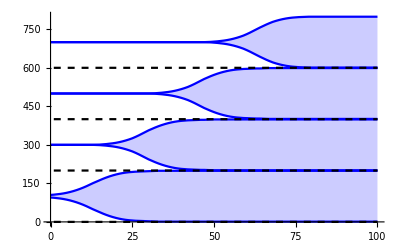

```mathematica
Show[Table[ListLinePlot[{Table[{t,(p-1/2)(κ/.Pars)+n[p,t]/2},{t,0,tmax/.Pars}],Table[{t,(p-1/2)(κ/.Pars)-n[p,t]/2},{t,0,tmax/.Pars}]},Filling->{1->{{2},Directive[Blue,Opacity[0.2]]}},PlotStyle->{Blue,Blue},PlotRange->{0,nd*κ/.Pars}],{p,1,nd/.Pars}],Plot[Table[κ(p-1)/.Pars,{p,1,nd/.Pars}],{t,1,tmax/.Pars},PlotStyle->Directive[Black,Dashed]]]
```

## Predicted coalescent times (Austerlitz et al.)

Given the order of our life cycle the resulting expressions for the coalescent probabilities are much simpler than in Austerlitz

Let x[i_,j_,t_] be the probability that a lineage in population i was in population j the previous time step.  Let m[k,t] be the population size of deme k after migration but before mating. In other words a life cycle (census)n[k,t-1]->(migration)nn[k,t]->(mating)n[k,t].

```mathematica
Clear[m]
```

```mathematica
nn[k_,t_]:=Block[{d},d=nd/.Pars;If[k==1,n[1,t-1](1-m/2)+n[2,t-1](m/2),If[k==d,n[d,t-1](1-m/2)+n[d-1,t-1](m/2),n[k,t-1](1-m)+n[k-1,t-1](m/2)+n[k+1,t-1](m/2)]]]
```

```mathematica
x[i_,j_,t_]:=Block[{d},d=nd/.Pars;If[j==i-1||j==i+1,(n[j,t-1] m/2)/nn[i,t],If[i==j,If[i==1||i==d,(n[i,t-1](1-m/2))/nn[i,t],(n[i,t-1](1-m))/nn[i,t]],0]]]/.Pars
```

```mathematica
x[4,4,49]
```

0.616099

Let P[i_,j_,t_,s_] be the probability that lineages in populations sampled in i and j at time t coalesce exactly s generations ago

```mathematica
P[i_,j_,t_,s_]:=Block[{d},d=nd/.Pars;
If[s==1,Sum[If[n[k,t-1]>0,x[i,k,t]x[j,k,t] 1/(2n[k,t-1]),0],{k,1,d}],
Sum[If[k==l,If[n[k,t-1]>0,x[i,k,t]x[j,l,t]P[k,l,t-1,s-1](1-1/(2 n[k,t-1])),0],x[i,k,t]x[j,l,t]P[k,l,t-1,s-1]],{k,1,d},{l,1,d}] 
]
]//N
```

The expected coalescent times are therefore

## Fst

From a coalescent standpoint Fst=T̄-OverBar[T_0]/T̄ where T̄ is the expected coalescent time between any two lineages in the metapopulation and OverBar[T_0] is the expected time for pairs drawn from the same deme.